# Inlämningsuppgift Algebra och Geometri

Malcolm Liljedahl, IX1303, malcolml@kth.se

Uppgifter

### Uppgift 2

Bestäm vinkeln mellan vektorerna  a = 2i - 2j - 2k 
							   b = 3i - 2j - k
En enkel lösning här var att använda VectorAngle funktionen för att få fram vinkeln mellan a och b.

```mathematica
VectorAngle[{2, -2, -2},{3,-2 ,-1}]
```

ArcCos[√(6/7)]

```mathematica
Reduce[ArcCos[√(6/7)]]
```

Reduce[ArcCos[√(6/7)]]

Jag kände att svaret ovan må stämma men det säger inte så mycket, därför så passar det bra med en grafisk illustration av svaret vilket ges via Graphics3D funktionen.

```mathematica
Graphics3D[{Thick,Line[{{0,0,0},{2, -2, -2}}],Line[{{0,0,0},{3,-2 ,-1}}]}]
```

-Graphics3D-

Här omvandlar jag ifrån radianer till grader.

```mathematica
N[ArcCos[√(6/7)]/Degree]
```

22.2077

Vinklen mellan vektorerna är: ArcCos[√(6/7)]eller 22.2° grader.

### Uppgift 4

Givet vektorerna u = 2i + 3j - 2k, v = 4i - j - k och w = -4i - j + 2k, beräkna vektortrippelprodukten u × (v × w)

```mathematica
u={2,3,-2}
v={4,-1,-1}
w= {-4,-1,2}
```

{2,3,-2}

{4,-1,-1}

{-4,-1,2}

För denna uppgift så kunde jag använda den inbygga crossproduct funktionen i mathematica. Först så använder jag det mellan v och w och sen så gör jag detsamma mellan resultat 
vektorn och u.

```mathematica
z  = Cross[v,w] //TensorReduce
```

{-3,-4,-8}

```mathematica
Cross[z,u] //TensorReduce
```

{32,-22,-1}

Vektortrippelprodukten är 32i - 22j - k.

### Uppgift 7

Givet matriserna A, B och C beräkna i.) A-B+C, ii.) ABC , iii.) CBA

```mathematica
a = mat = {{3,2,4},{7,12,0},{2,5,2}}//MatrixForm
b = mat = {{5,8,7},{6,4,9},{10,1,0}}//MatrixForm
c = mat = {{5,22,5},{5,9,7},{6,8,2}} //MatrixForm
```

(3 | 2 | 4
7 | 12 | 0
2 | 5 | 2)

(5 | 8 | 7
6 | 4 | 9
10 | 1 | 0)

(5 | 22 | 5
5 | 9 | 7
6 | 8 | 2)

i.)

```mathematica
a-b +c
```

```mathematica
({{3, 2, 4}, {7, 12, 0}, {2, 5, 2}})-({{5, 8, 7}, {6, 4, 9}, {10, 1, 0}})+({{5, 22, 5}, {5, 9, 7}, {6, 8, 2}})//MatrixForm
```

(3 | 16 | 2
6 | 17 | -2
-2 | 12 | 4)

Efter aritmetiken så slutar vi upp med matrisen:

(3 | 16 | 2
6 | 17 | -2
-2 | 12 | 4)

ii.)

```mathematica
a*b*c
```

```mathematica
({{3, 2, 4}, {7, 12, 0}, {2, 5, 2}}) ({{5, 8, 7}, {6, 4, 9}, {10, 1, 0}}) ({{5, 22, 5}, {5, 9, 7}, {6, 8, 2}})//MatrixForm
```

(75 | 352 | 140
210 | 432 | 0
120 | 40 | 0)

Efter aritmetiken så slutar vi upp med matrisen:

(75 | 352 | 140
210 | 432 | 0
120 | 40 | 0)

iii.)

```mathematica
c*b*a
```

```mathematica
({{3, 2, 4}, {7, 12, 0}, {2, 5, 2}}) ({{5, 8, 7}, {6, 4, 9}, {10, 1, 0}}) ({{5, 22, 5}, {5, 9, 7}, {6, 8, 2}})//MatrixForm
```

(75 | 352 | 140
210 | 432 | 0
120 | 40 | 0)

Efter aritmetiken så slutar vi upp med matrisen:

(75 | 352 | 140
210 | 432 | 0
120 | 40 | 0)

### Uppgift 9

Hitta egenvärdena till matrisen

A = (9 | -4 | -2 | -4
-56 | 32 | -28 | 44
-14 | -14 | 6 | -14
42 | -33 | 21 | -45)

Här är det smidigt att använda mathematicas inbyggda Eigenvalues funktion.

```mathematica
a= mat = {{9,-4,-2,-4},{-56,32,-28,44},{-14,-14,6,-14},{42,-33,21,-45}} //MatrixForm
```

(9 | -4 | -2 | -4
-56 | 32 | -28 | 44
-14 | -14 | 6 | -14
42 | -33 | 21 | -45)

```mathematica
Eigenvalues[a]
```

```mathematica
Eigenvalues[({{9, -4, -2, -4}, {-56, 32, -28, 44}, {-14, -14, 6, -14}, {42, -33, 21, -45}})]
```

{13,13,-12,-12}

Egenvärdena till matrisen a är 13, 13, -12, -12.

### Uppgift 18

Ange diagonalmatrisen D och matriserna P och P-1 som används för diagonalisering av A.

```mathematica
a = ({{-6, 4, 0, 9}, {-3, 0, 1, 6}, {-1, -2, 1, 0}, {-4, 4, 0, 7}})
```

{{-6,4,0,9},{-3,0,1,6},{-1,-2,1,0},{-4,4,0,7}}

Steg 1 här är att ta fram egenvärdena, vilket kan göras via det inbyggda verktyget Eigenvalues. Vi combinerar det med att både ta fram D och P.

```mathematica
d= DiagonalMatrix[Eigenvalues[a]]
```

{{5,0,0,0},{0,-2,0,0},{0,0,-2,0},{0,0,0,1}}

```mathematica
p=Transpose[Eigenvectors[a]]
```

{{2,6,1,2},{1,-3,1,-1},{-1,0,1,-7},{2,4,0,2}}

Nu kan vi inversa p via verktyget inverse och sen multiplicera det med p och d.

```mathematica
p.d.Inverse[p]//MatrixForm
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

Här kan vi se att svaret vi fick ut är detsamma som urssprungsmatrisen A.

### Uppgift 13

Visa att matrisen A är en reguljär övergångsmatris och beräkna jämviktsverktorn.

```mathematica
a = ({{0.4, 0.2, 0.7}, {0, 0.6, 0.1}, {0.6, 0.2, 0.2}})
```

{{0.4,0.2,0.7},{0,0.6,0.1},{0.6,0.2,0.2}}

i.) Visa att matrisen är en reguljär övergångsmatris.

Detta görs genom att vi bevisar att det finns ett tal n som gör att A^n  innehåller endast nollskilda element.

```mathematica
a^3//MatrixForm
```

(0.064 | 0.008 | 0.343
0 | 0.216 | 0.001
0.216 | 0.008 | 0.008)

Här kan vi se att alla tal förutom det som ursprungligen var 0 är nollskillda då matrisen är upphöjd med 3.

ii.) Beräkna jämviktsverktorn.

Detta görs genom att lösa (A-I)x = 0, vi använder oss av Sarrus regel.

```mathematica
i= ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
```

```mathematica
d = ({{0.4, 0.2, 0.7}, {0, 0.6, 0.1}, {0.6, 0.2, 0.2}}) - ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}) //MatrixForm
```

(-0.6 | 0.2 | 0.7
0 | -0.4 | 0.1
0.6 | 0.2 | -0.8)

Som vi sen radreducerar:

```mathematica
RowReduce[({{-0.6, 0.2, 0.7, 0}, {0, -0.4, 0.1, 0}, {0.6, 0.2, -0.8, 0}})]//MatrixForm
```

(1 | 0. | -1.25 | 0.
0 | 1 | -0.25 | 0.
0 | 0 | 0 | 0)

x = 1.25z
y = 0.25z   -> (1.25
0.25
1)
z = 1 (fri)

```mathematica
Rationalize[({{1.25}, {0.25}, {1}})]
```

{{5/4},{1/4},{1}}

Vi ger z värdet 4, så vi kan bilda en bas utan bråk, då blir vår nya bas:

```mathematica
w = {5},{1},{4} -> ({{5}, {1}, {4}})
```

### Uppgift 8

Hitta den radreducerade trappstegsmatrisen (rref) till matrisen. Har matrisen någon redundans?

```mathematica
a = ({{2, 4, 8}, {4, 5, 1}, {7, 9, 3}})
```

```mathematica
a = ({{2, 4, 8}, {4, 5, 1}, {7, 9, 3}})
```

{{2,4,8},{4,5,1},{7,9,3}}

För att radreducera denna matris så kan jag utnyttja den inbyggda funktionen RowReduce.

```mathematica
RowReduce[a]//MatrixForm
```

(1 | 0 | -6
0 | 1 | 5
0 | 0 | 0)

Ja matrisen har redundans då den tredje kolumnen består av multiplar av den första och den andra. Den första kolumnen kan multipliceras med -6 och den andra kan multipliceras med 5 för att få kolumn 3.

### Uppgift 10

Visa att kolumnerna i matris A är ortogonala.

A = (-6 | -3 | 6 | 1
-1 | 2 | 1 | -6
3 | 6 | 3 | -2
6 | -3 | 6 | -1
2 | -1 | 2 | 3
-3 | 6 | 3 | 2
-2 | -1 | 2 | -3
1 | 2 | 1 | 6)

```mathematica
a = mat = {{-6,-3,6,1},{-1,2,1,-6},{3,6,3,-2},{6,-3,6,-1},{2,-1,2,3},{-3,6,3,2},{-2,-1,2,-3},{1,2,1,6}} //MatrixForm
```

(-6 | -3 | 6 | 1
-1 | 2 | 1 | -6
3 | 6 | 3 | -2
6 | -3 | 6 | -1
2 | -1 | 2 | 3
-3 | 6 | 3 | 2
-2 | -1 | 2 | -3
1 | 2 | 1 | 6)

För att visa att kolumnerna är ortogonala så kan vi använda theorem 6 vilket lyder att vi ska beräkna A^T*A. Så vi börjar med att beräkna A^T vilket kan göras vi den inbyggda funktionen Transpose

```mathematica
b = Transpose[{{-6,-3,6,1},{-1,2,1,-6},{3,6,3,-2},{6,-3,6,-1},{2,-1,2,3},{-3,6,3,2},{-2,-1,2,-3},{1,2,1,6}} ] // MatrixForm
```

(-6 | -1 | 3 | 6 | 2 | -3 | -2 | 1
-3 | 2 | 6 | -3 | -1 | 6 | -1 | 2
6 | 1 | 3 | 6 | 2 | 3 | 2 | 1
1 | -6 | -2 | -1 | 3 | 2 | -3 | 6)

Nu kan vi multiplicera A^T*A

```mathematica
Dot[b,a]
```

(-6 | -1 | 3 | 6 | 2 | -3 | -2 | 1
-3 | 2 | 6 | -3 | -1 | 6 | -1 | 2
6 | 1 | 3 | 6 | 2 | 3 | 2 | 1
1 | -6 | -2 | -1 | 3 | 2 | -3 | 6).(-6 | -3 | 6 | 1
-1 | 2 | 1 | -6
3 | 6 | 3 | -2
6 | -3 | 6 | -1
2 | -1 | 2 | 3
-3 | 6 | 3 | 2
-2 | -1 | 2 | -3
1 | 2 | 1 | 6)

```mathematica
({{-6, -1, 3, 6, 2, -3, -2, 1}, {-3, 2, 6, -3, -1, 6, -1, 2}, {6, 1, 3, 6, 2, 3, 2, 1}, {1, -6, -2, -1, 3, 2, -3, 6}}).({{-6, -3, 6, 1}, {-1, 2, 1, -6}, {3, 6, 3, -2}, {6, -3, 6, -1}, {2, -1, 2, 3}, {-3, 6, 3, 2}, {-2, -1, 2, -3}, {1, 2, 1, 6}})//MatrixForm
```

(100 | 0 | 0 | 0
0 | 100 | 0 | 0
0 | 0 | 100 | 0
0 | 0 | 0 | 100)

Då vi här har tal på diagonalen med resten är 0 tyder på våran product matris är en identitetsmatris vilket innebär att kolumnerna i A ortogonala.

### Uppgift 12

The actual color a viewer sees on a screen is influenced by the specific type and amount of phosphors on the screen.
So each computer screen manufacturer must convert between the (R, G, B) data and an international CIE standard for color,
which uses three primary colors, called X, Y, and Z. A typical conversion for short-persistence phosphors is

(0.61 | 0.29 | 0.150
0.35 | 0.59 | 0.063
0.04 | 0.12 | 0.787)(R
G
B) = (X
Y
Z)

A computer program will send a stream of color information to the screen, using standard CIE data (X, Y, Z). Find the
equation that converts these data to the (R, G, B) data needed for the screen’s electron gun.

Ekvationen är av form Ax = y vilket gör att vi kan skriva om den till x = (A^-1)y

```mathematica
a = ({{0.61, 0.29, 0.150}, {0.35, 0.59, 0.063}, {0.04, 0.12, 0.787}})
```

{{0.61,0.29,0.15},{0.35,0.59,0.063},{0.04,0.12,0.787}}

```mathematica
Inverse[a]//MatrixForm
```

(2.25855 | -1.03951 | -0.347261
-1.34954 | 2.3441 | 0.0695708
0.090981 | -0.304589 | 1.27769)

Svaret blir då:

(R
G
B) = (2.25855 | -1.03951 | -0.347261
-1.34954 | 2.3441 | 0.0695708
0.090981 | -0.304589 | 1.27769)(X
Y
Z)

### Uppgift 5

Lös grafiskt ekvationssystemet: 	x - 2y = 3     dvs plotta planen och se om det finns någon lösning.
								3x + 5y = 17

x - 2y = 3 ->  y =  x/2-3/2
3x + 5y = 17 ->  y =  17/5-(3x)/5

```mathematica
f[x_] = x/2-3/2
g[x_] = 17/5-(3x)/5
```

-3/2+x/2

17/5-(3 x)/5

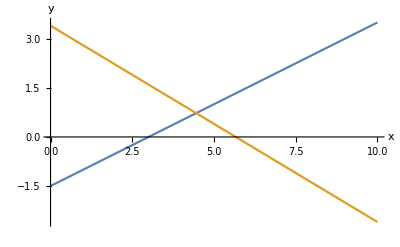

```mathematica
Graf1[x_] :=f[x]
Graf2[x_] := g[x]
Plot[{Graf1[x], Graf2[x]}, {x,0,10}, AxesLabel->{"x","y"}]
```

Lösning på detta ekvationsystem är:

```mathematica
FindRoot[Graf1[x]==Graf2[x], {x, 5}]
```

{x→4.45455}

```mathematica
y=x/2-3/2 = 4.454545454545455/2-3/2
```

0.727273

x = 4.45455
y = 0.727273

Lösningen på detta ekvationssystem är skärnngspunkten mellan graferna vilket sker runt (4.5, 0.7)

Referenser

## Referenser

https://reference.wolfram.com/language/ref/IdentityMatrix.html 
https://reference.wolfram.com/language/ref/Eigenvectors.html 
https://reference.wolfram.com/language/ref/DiagonalMatrix.html 
https://reference.wolfram.com/language/ref/Eigenvalues.html 
https://mathworld.wolfram.com/BAC-CABIdentity.html 
https://reference.wolfram.com/language/ref/Inverse.html 
https://math.stackexchange.com/questions/2781510/how-do-i-solve-ax-y-using-this-decomposition
https://math.berkeley.edu/~mgu/MA54/hw4sol.pdf 
https://en.wikipedia.org/wiki/Orthogonal_matrix#:~:text=A%20real%20square%20matrix%20is,orthonormal%20basis%20of%20%E2%84%9Dn.